# Chapter 2 Importing and Exporting Data

Often we have data on a disk and want to read it into Mathematica. The data can be either in an ASCII representation or in a binary format. This chapter discusses techniques to read such data files.

In addition to a discussion of using built - in Mathematica commands to handle these tasks, Sections 2.1 and 2.2 also introduce some EDA functions specifically designed to import and export data in ASCII files.

Section 2.3 discusses reading binary data files and Section 2.4 discusses ways to get a scanned plot of data into Mathematica.

## 2.1 Importing Data from an ASCII File

Most existing data acquisition software is capable of producing a file containing an ASCII representation of a data set. This section discusses techniques to read such a file into Mathematica, and introduces the ImportData function that often contains only the options needed to read such a file.

The first subsection is an introduction to the ImportData function, and also discusses using the built - in command ReadList function to read a data file.

The next subsection illustrates the use of ImportData using a real - world example.

The final subsection summarizes the ImportData function.

### 2.1 .1 Introduction

Suppose we have a file named data1.txt.  (Note :  The examples in this section assume the existence of a file data in your current working directory. This file is not actually provided with EDA. Thus, input commands of this section are illustrative and will not actually work unless you have the specified data files.)

```mathematica
FilePrint["data1.txt"]
```

1
2
3
4
5
6
7
8

We can read the file with the built - in ReadList command.

```mathematica
mydata=ReadList["data1.txt"]
```

{1,2,3,4,5,6,7,8}

Many built - in Mathematica functions, and all those in Experimental Data Analyst, will treat this as a set of eight values of the dependent variable.

The ImportData program that is included in EDA can also read this file.

```mathematica
Needs["EDA`"]
```

```mathematica
mydata=ImportData["data1.txt"]
```

{1.,2.,3.,4.,5.,6.,7.,8.}

Say instead that data has two columns of numbers.

```mathematica
FilePrint["data2.txt"]
```

1.23	2.45
4.56	17.54
5.67	26.45

We read the file with ReadList.

```mathematica
mydata=ReadList["data2.txt"]
```

{3.0135,79.9824,149.972}

What has happened is that ReadList has interpreted each line of the file as a multiplication of two numbers, which Mathematica has evaluated. This can be suppressed by telling ReadList to read numbers.

```mathematica
mydata=ReadList["data2.txt",Number]
```

{1.23,2.45,4.56,17.54,5.67,26.45}

If the numbers in the file represent {x, y} pairs, we can have ReadList handle each line separately by setting RecordLists to True.

```mathematica
mydata=ReadList["data2.txt",Number,RecordLists->True]
```

{{1.23,2.45},{4.56,17.54},{5.67,26.45}}

This is just the format expected by many Mathematica functions such as Fit and ListPlot and by Experimental Data Analyst.

ImportData handles this case automatically.

```mathematica
mydata=ImportData["data2.txt"]
```

{{1.23,2.45},{4.56,17.54},{5.67,26.45}}

To have ImportData treat each number in the file as a value for the dependent variable, we can use the OutputVariables option.

```mathematica
mydata=ImportData["data2.txt",OutputVariables->1]
```

{1.23,2.45,4.56,17.54,5.67,26.45}

We can tell ImportData to treat the numbers as a succession of {x, { y, erry}} values.

```mathematica
mydata=ImportData["data2.txt",OutputVariables->3]
```

{{1.23,{2.45,4.56}},{17.54,{5.67,26.45}}}

Imagine the file contains three numbers per line.

```mathematica
FilePrint["data3.txt"]
```

1	2	.5
3	4	.6
5	6	.7
7	8	.8

By default, ImportData will treat each line as a data point, and since there are three values for each point, it will assume that they are {x, {y, erry}} values.

```mathematica
mydata=ImportData["data3.txt"]
```

{{1.,{2.,0.5}},{3.,{4.,0.6}},{5.,{6.,0.7}},{7.,{8.,0.8}}}

If the final number in each line is the error associated with the first number, then the UseVariables option can be used.

```mathematica
mydata=ImportData["data3.txt",UseVariables->{2,1,3}]
```

{{2.,{1.,0.5}},{4.,{3.,0.6}},{6.,{5.,0.7}},{8.,{7.,0.8}}}

The UseVariables option can also be used to select only some of the numbers on each line.

```mathematica
mydata=ImportData["data3.txt",UseVariables->{2,3}]
```

{{2.,0.5},{4.,0.6},{6.,0.7},{8.,0.8}}

Since we have extracted two numbers per record, ImportData assumes they are {x, y} pairs. We can tell the program that the assumption is wrong.

```mathematica
mydata=ImportData["data3.txt",UseVariables->{2,3},OutputVariables->4]
```

{{{2.,0.5},{4.,0.6}},{{6.,0.7},{8.,0.8}}}

Now each data point consists of {{x, errx}, {y, erry}} values.

Sometimes a data file is not “flat”.

```mathematica
FilePrint["data4.txt"]
```

1	2
3
4
5	6	7	8

We can tell ImportData to treat the numbers as pairs.

```mathematica
mydata=ImportData["data4.txt",InputVariables->2]
```

{{1.,2.},{3.,4.},{5.,6.},{7.,8.}}

We can extract the first of each pair.

```mathematica
mydata=ImportData["data4.txt",InputVariables->2,UseVariables->{1}]
```

{1.,3.,5.,7.}

We can then put these numbers into {x, y} pairs.

```mathematica
mydata=ImportData["data4.txt",InputVariables->2,UseVariables->{1},OutputVariables->2]
```

{{1.,3.},{5.,7.}}

By default, ImportData assumes that either spaces or tabs separate the numbers in each row. If this is not a correct assumption, as in a data file that uses commas to separate the numbers, we can use the WordSeparators option.

```mathematica
FilePrint["data5.txt"]
```

1.2, 3.2e17
2.4, .7
12353E-2, 151.2, 3.2e17
2.4, .7
12353E-2, 151.2, 3.2e17
2.4, .7
12353E-2, 15

```mathematica
mydata=ImportData["data5.txt",WordSeparators->{","}]
```

{{1.2,3.2×10^17},{2.4,0.7},{123.53,15.}}

Of course, the other options to ImportData can be used also.

```mathematica
mydata=ImportData["data5.txt",WordSeparators->{","},OutputVariables->3]
```

{{1.2,{3.2×10^17,2.4}},{0.7,{123.53,15.}}}

Sometimes a data file is not all numbers.

```mathematica
FilePrint["data6.txt"]
```

charley 17.1
joe 8
peter 42
sam 17.2

To extract the numbers from this with ReadList would require ReadList["data", Word], extracting the numeric parts which will be represented as strings, and converting the strings to numbers. ImportData provides an AllNumeric option which, if set to False, does all this automatically.

```mathematica
mydata=ImportData["data6.txt",AllNumeric->False,UseVariables->{2}]
```

{17.1,8.,42.,17.2}

This has the correct numeric types.

```mathematica
NumberQ/@mydata
```

{True,True,True,True}

Our final introductory data set contains a header and a trailer.

```mathematica
FilePrint["data7.txt"]
```

Header for this data set

x y erry
--------
1 2 .5
3 4 .6
5 6 .7
7 8 .8
-------
This data was taken by the
analog-analog converter at
the University of Toronto.

There are four lines of header that include one blank line and four lines of trailer information after the data.

We can still use ReadList, but we need to skip the header and tell it to read only 12 numbers.

```mathematica
strm=OpenRead["data7.txt"];
Skip[strm,Record,4,NullRecords->True];
mydata=ReadList[strm,Number,12,RecordLists->True]
Close[strm];
```

{{1,2,0.5},{3,4,0.6},{5,6,0.7},{7,8,0.8}}

The NullRecords option to Skip causes it to count the blank lines; without it the first line of data would have been lost and ReadList would have tried to read the first line of the trailer. The Close at the end is good practice to avoid having too many open files at once.

Note that to use this data for analysis, some further partitioning may be necessary.

ImportData can read the same file.

```mathematica
mydata=ImportData["data7.txt",HeaderLines->4,NumData->12]
```

{{1.,{2.,0.5}},{3.,{4.,0.6}},{5.,{6.,0.7}},{7.,{8.,0.8}}}

Of course, the other options to ImportData can be used to massage the output format.

Another way to use ImportData to handle this file is to use the TrailerLines option. Since the trailer contains nonnumerics, and the trailer lines are removed after the data has been read using ReadList, we must set AllNumeric to False.

```mathematica
ImportData["data7.txt",HeaderLines->4,AllNumeric->False,TrailerLines->4]
```

{{1.,{2.,0.5}},{3.,{4.,0.6}},{5.,{6.,0.7}},{7.,{8.,0.8}}}

The formatting of the data into {x,{y, erry}} triples can be suppressed.

```mathematica
ImportData["data7.txt",HeaderLines->4,AllNumeric->False,TrailerLines->4,FormatData->False]
```

{{1.,2.,0.5},{3.,4.,0.6},{5.,6.,0.7},{7.,8.,0.8}}

This returns each data point as a flat list of numbers. The FormatData option only has an effect for data sets with three or four variables.

Sometimes the data set has more than four variables.

```mathematica
FilePrint["data8.txt"]
```

1 2 3 4 5 6
11 12 13 14 15 16
21 22 23 24 25 26
31 32 33 34 35 36

Then ImportData returns a flat list.

```mathematica
ImportData["data8.txt"]
```

{{1.,2.,3.,4.,5.,6.},{11.,12.,13.,14.,15.,16.},{21.,22.,23.,24.,25.,26.},{31.,32.,33.,34.,35.,36.}}

### 2.1.2 A Real-World Example

Aptec Engineering, Inc. manufactures analog-digital converters and software that turns a standard PC into a nuclear multichannel analyzer. A spectrum was taken with the analyzer and saved as an ASCII print file called orig.dat.

In this example, Mathematica was running on a Hewlett-Packard UNIX computer, and the PC was on the ether network using Sun Microsystems’ PC-NFS. The orig.dat file was saved on the Hewlett-Packard disk in the area that PC-NFS treats as a local DOS disk. Most UNIX platforms offer a program to convert files from DOS to UNIX; on the Hewlett-Packard machine, it is called dos2ux and was run under UNIX.

$ dos2ux orig.dat > Aptec.txt

Note that this Aptec.txt file is shipped as part of EDA and is in the Data subdirectory. To make use of this data file, you need to set the current directory to this Data subdirectory. This can be accomplished using the command SetDirectory[directory name].

Here is a summary of the file.

```mathematica
FilePrint["Aptec.txt"]
```

Aptec PC/MCA - HPS Show  June 30-July 3
                               Aug/4/1994 12:03:47
****** 65 lines omitted from the header listing *******
  Channel Energy    MeV   Counts
  ------- ------------- ---------- ---------- ---------- ---------- ----------
      0       -0.07              0          0          0          0          0
      5       -0.06              0          0          0          0          0
     10       -0.05              0          0          0          0          0
     15       -0.04              0          0          0          0          0
     20       -0.03              0          0          0          0          0
     25       -0.02              0          0          0          0          0
     30       -0.01              0          0          0          0          0
     35       -0.01              0          0          0          3          0
     40        0.00              0          0       2038       4175       3668
     45        0.01           3560       3566       3593       3452       3397
     50        0.02           3321       3291       3386       3155       3173
   ****** 801 lines omitted from the data listing ******
   4060       47.65              0          0          0          0          0
   4065       48.00              0          0          0          0          0
   4070       48.35              0          0          0          0          0
   4075       48.69              0          0          0          0          0
   4080       49.05              0          0          0          0          0
   4085       49.40              0          0          0          0          0
   4090       49.75              1          0          0          0          0
   4095       50.11              0

Note that in the display, we have omitted a number of lines in the header and from the data. Also note that each line of data consists of seven numbers, of which columns 3, 4, 5, 6, and 7 are the counts. Finally, the last line of data contains fewer numbers than the others; by default ImportData pads the last line with zeros, which is reasonable in this case.

We read the counts from the file.

```mathematica
counts=ImportData["Aptec.txt",HeaderLines->69,OutputVariables->1,UseVariables->{3,4,5,6,7}];
```

ImportData::padding: Warning: padding the last line with 4 zeros.

We can examine the result using Short and EDAListPlot.

```mathematica
Short[counts,10]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.,0.,0.,0.,2038.,4175.,3668.,3560.,3566.,3593.,3452.,3397.,3321.,3291.,3386.,3155.,3173.,3139.,3146.,3114.,3118.,3007.,3031.,3054.,2978.,2981.,2887.,2919.,2951.,2995.,2948.,2882.,2951.,2873.,2881.,2896.,2963.,2898.,«3948»,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

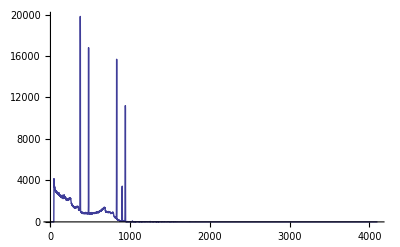

```mathematica
EDAListPlot[counts,Joined->True,PlotRange->All]
```

We see that the region for channels above 1000 is not of great interest.

We can extract the first 1000 counts.

```mathematica
counts=Take[counts,1000];
```

We can also use ImportData to read the file again to get the first 1000 counts, which is the first 200 lines. Recall that each line contains 7 numbers of which we will use only the last 5.

```mathematica
counts=ImportData["Aptec.txt",HeaderLines->69,NumData->1400,UseVariables->{3,4,5,6,7},OutputVariables->1];
```

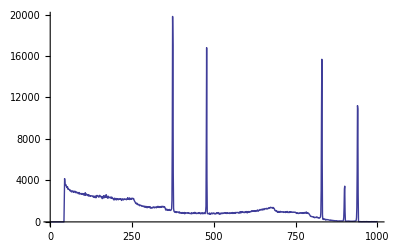

```mathematica
EDAListPlot[counts,Joined->True,PlotRange->All]
```

We extract the channel/energy data.

```mathematica
energy=ImportData["Aptec.txt",HeaderLines->69,OutputVariables->2,UseVariables->{1,2}];
```

ImportData::padding: Warning: padding the last line with 4 zeros.

Rather than make an assumption about the functional relationship between channel and energy, we can simply form an interpolation.

```mathematica
energyInterpolation=Interpolation[energy];
```

The energy versus channel plot is interesting.

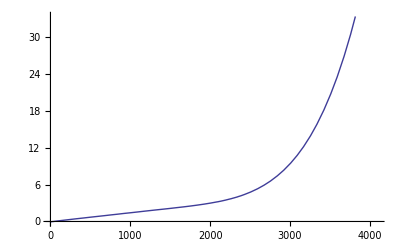

```mathematica
Plot[energyInterpolation[channel], {channel, 1, 4095}]
```

Evidently the analog-digital converter and/or counter is highly nonlinear at the higher channels, although quite linear for the first 1000 or so.

We then evaluate for the first 1000 channels.

```mathematica
energy=Table[energyInterpolation[i],{i,1,1000}];
```

Finally, we can form a list of {energy, counts} pairs.

```mathematica
counts=Transpose[{energy,counts}];
```

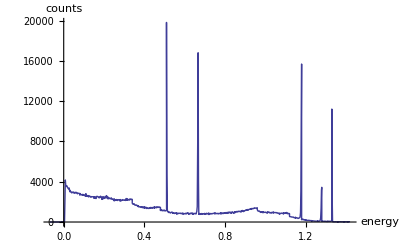

```mathematica
EDAListPlot[counts,AxesLabel->{"energy","counts"},Joined->True,PlotRange->All]
```

### 2.1.3 Summary of ImportData

This section provides a summary of the ImportData function. First, it lists the usage message for the function and all its options. Then it sketches how the function works, and in particular the order in which the options are processed.

```mathematica
?ImportData
```

ImportData[file] reads an ASCII file and returns a dataset. The
	'file' is assumed to be in the current directory. ImportData[file,
	directory] reads 'file' in 'directory'.

```mathematica
TableForm[Options[ImportData]]
```

AllNumeric→True
FormatData→True
InputVariables→Automatic
HeaderLines→0
NumData→All
OutputVariables→Automatic
TrailerLines→0
UseVariables→Automatic
WordSeparators→{ ,	}

```mathematica
?AllNumeric
```

AllNumeric is an option to ImportData. If AllNumeric is set to the default
	(True), the file (excluding any headers), is assumed to be all numerics.
	If set to False, then the file can contain words, as well as numbers.
	In this case, ImportData will run more slowly.

```mathematica
?FormatData
```

FormatData is an option to ImportData that specifies if the
	returned data is formatted according to the specification of the
	Experimental Data Analyst. When set to True (the default) with
	either three or four variables in the data set, the returned
	data is formatted. When set to False or there are exactly
	two or more than four variables in the data set, then each
	data point is returned as a flat list.

```mathematica
?HeaderLines
```

HeaderLines is an option to ImportData that specifies the number of
	lines at the beginning of the file that include header information and
	should be skipped. If set to 0 (the default), no initial lines are
	skipped. Blank lines are counted.

```mathematica
?InputVariables
```

InputVariables is an option to ImportData that specifies the number
	of variables in the input dataset. If Automatic (the default), each
	line of the input file is assumed to be a data point and the number of
	variables is calculated by the amount of data in the first line
	of the input file.

```mathematica
?NumData
```

NumData is an option to ImportData that specifies the amount of
	data to be read. If set to All (the default), all data
	is read.

```mathematica
?OutputVariables
```

OutputVariables is an option to ImportData that specifies the
	number of variables to be output. If Automatic (the default), it
	is equal to the number of input variables.

```mathematica
?TrailerLines
```

TrailerLines is an option to ImportData that specifies the number of
	lines at the end of the file that do not contain data and should
	be ignored. If set to 0 (the default), no trailer lines are
	ignored. In all cases, blank lines are ignored in counting the number
	of lines. If AllNumeric is set to True (the default), lines containing
	non-numbers are also ignored in counting and a warning message is
	generated. If AllNumeric is set to False, all lines except blank
	ones are counted.

```mathematica
?UseVariables
```

UseVariables is an option to ImportData that specifies the fields
	in the input records that are to be extracted and used in the
	output record. The values are extracted in the order in which
	they are given in the list.

```mathematica
?WordSeparators
```

WordSeparators is an option for Read, Find and related functions which specifies the list of strings to be taken as delimiters for words.

The "More..." button in the previous output is a link for further information on this option.

Finally, here is the order in which ImportData processes options.

1. If WordSeparators is not set to the default of {" ", "\t"}, then the AllNumeric option is set to False. This change is necessary, but it does slow down ImportData somewhat.

2. HeaderLines, if any, are skipped using Skip.

3. ImportData uses the built-in command ReadList, with the RecordLists option set to True. If the AllNumeric option is set to True (the default) it uses type Real; otherwise it uses type Word. If the NumData option is All (the default) it reads until the end of file; otherwise it reads NumData objects.

4. TrailerLines is set to a number, than that number of lines is then dropped from the end of the data. Note that blank lines are not counted, since ReadList has not set NullRecords to True.

5. InputVariables is set to a number, the data is then formatted into records of InputVariables numbers each.

6. The last line of the data is padded if necessary so it has the same number of variables as the first line.

7. If UseVariables is not All, fields specified by it are then extracted, forming records of length Length[UseVariables].

8. If OutputVariables is not Automatic, the data is then formatted into records of length equal to its value.

9. If the AllNumeric option is not set to  True, the fields, currently represented as strings, are converted to numbers.

10. Unless FormatData is set to False, the data is formatted into the standard form expected by Experimental Data Analyst.

## 2.2 Exporting Data to an ASCII File

In this section we discuss techniques to create a file containing an ASCII representation of a data set.

The first subsection introduces the EDA function ExportData and also discusses the built-in functions Write and WriteString.

The final subsection summarizes the ExportData function.

### 2.2.1 Introduction

Imagine we have a Mathematica data set.

```mathematica
mydata={1,2,3,4,5};
```

The set, including its name, can be saved into a file using the Mathematica command Save.

```mathematica
Save["data",mydata]
```

We can examine the contents of the file.

```mathematica
FilePrint["data"]
```

mydata = {1, 2, 3, 4, 5}

Warning: if the file data already exists in the current directory, the Save command will append the definition to it. Also, some versions of the front end interface have the current directory set to a system area of the disk by default, which may not be where you wish to save your work files. You can determine your current directory with the Directory command. To change where your work files are saved, you can specify an absolute pathname for data or else reset the current directory with SetDirectory.

We remove mydata from the Mathematica session.

```mathematica
Clear[mydata];
```

Now we can read the file back in to redefine mydata.

```mathematica
<<"data";
```

```mathematica
mydata
```

{1,2,3,4,5}

The Mathematica command Write allows us to save the contents of mydata without the associated variable name.

```mathematica
strm=OpenWrite["data"];
```

```mathematica
Write[strm,mydata]
```

```mathematica
Close[strm];
```

```mathematica
FilePrint["data"]
```

{1, 2, 3, 4, 5}

Warning: If the file data already exists in the current directory OpenWrite will truncate it to size zero. The EDA function ExportData, introduced later in this section, will not overwrite an existing file unless the defaults to the function are changed.

If we wish the file to contain five rows, each containing one of the data, we can still use Write.

```mathematica
strm=OpenWrite["data"];
```

```mathematica
(Write[strm,#1]&)/@mydata;
```

```mathematica
Close[strm];
```

```mathematica
FilePrint["data"]
```

1
2
3
4
5

The built-in WriteString is more low-level than Write and can achieve the same effect.

```mathematica
strm=OpenWrite["data"];
```

```mathematica
(WriteString[strm,ToString[#1],"\n"]&)/@mydata;
```

```mathematica
Close[strm];
```

```mathematica
FilePrint["data"]
```

1
2
3
4
5

ExportData handles this operation automatically. First, we delete the file data we have created above.

```mathematica
DeleteFile["data"]
```

Now we write mydata into data using ExportData.

```mathematica
Needs["EDA`"]
```

```mathematica
ExportData["data",mydata]
```

```mathematica
FilePrint["data"]
```

1
2
3
4
5

Internally, ExportData uses WriteString.

Below we will be illustrating the use of ExportData, always writing into a file named data.  By default, ExportData will not overwrite an existing file.  An option Overwrite to ExportData, if set to True, will allow ExportData to overwrite existing files. Thus, we could have all calls to ExportData below include the option.

```mathematica
ExportData[ ... , Overwrite -> True]
```

This is certainly safe, but for our purposes we will use SetOptions to change the behavior of ExportData for the remainder of this session.

```mathematica
SetOptions[ExportData,Overwrite->True];
```

Say the data contains {x, y} pairs.

```mathematica
mydata={{1.234,3.4/10^5},{11.2,6.6/10^6},{21.2,9.01/10^2}}
```

{{1.234,0.000034},{11.2,6.6×10^-6},{21.2,0.0901}}

ExportData handles this case also.

```mathematica
DeleteFile["data"]
```

```mathematica
ExportData["data",mydata]
```

```mathematica
FilePrint["data"]
```

1.234	0.000034
11.2	6.5999999999999995*^-6
21.2	0.0901

Note that in the file the columns are separated by tabs and that the second number in the second row is represented in a form that Mathematica recognizes, but that some other programs may not.

We can change the separator between columns to, say, a comma followed by a space.

```mathematica
DeleteFile["data"]
```

```mathematica
ExportData["data",mydata,Separator->", "]
```

```mathematica
FilePrint["data"]
```

1.234, 0.000034
11.2, 6.5999999999999995*^-6
21.2, 0.0901

We can change the numbers to a form that Fortran and C can recognize.

```mathematica
DeleteFile["data"]
```

```mathematica
ExportData["data",mydata,DataForm->FortranForm]
```

```mathematica
FilePrint["data"]
```

1.234	0.000034
11.2	6.5999999999999995e-6
21.2	0.0901

Of course, the options can be combined.

```mathematica
DeleteFile["data"]
```

```mathematica
ExportData["data",mydata,DataForm->CForm,Separator->","]
```

```mathematica
FilePrint["data"]
```

1.234,0.000034
11.2,6.5999999999999995e-6
21.2,0.0901

Finally, the data set can contain { x, {y, erry}} values.

```mathematica
mydata={{-.12,{6.9999,6.888}},{1,{21,321}}}
```

{{-0.12,{6.9999,6.888}},{1,{21,321}}}

```mathematica
DeleteFile["data"]
```

```mathematica
ExportData["data",mydata]
```

```mathematica
FilePrint["data"]
```

-0.12	6.9999	6.888
1	21	321

Note that because of the representation of the numbers in the first row, this may not be what you need. Specifying a Padding option causes the function to use PaddedForm with the value of the option as its second argument.

```mathematica
DeleteFile["data"]
```

```mathematica
ExportData["data",mydata,Padding->{7,3}]
```

This produces a file that could be read easily by a Fortran program.

```mathematica
FilePrint["data"]
```

-0.120    7.000    6.888
    1.000   21.000  321.000

For the Fortran aficionado, Section 7.3 of W.T. Shaw and J. Tigg, Applied Mathematica: Getting Started, Getting It Done (Addison-Wesley, 1994) contains many helpful ideas.

### 2.2.2 Summary of ExportData

```mathematica
?ExportData
```

ExportData[file, data] writes data into a file. By default, the
	numbers are written in InputForm; a DataForm option can change InputForm
	to others such as FortranForm. By default the word separator is a
	tab unless Padding has been specified; a separator option can change
	a tab to an arbitrary string.

```mathematica
?DataForm
```

DataForm is an option to ExportData. It specifies the way that
	numbers are written. Valid values include InputForm (the default),
	FortranForm, and others.

```mathematica
?Overwrite
```

Overwrite is an option to ExportData. If Overwrite is set to False (the default) and the file to be written already exists in the current directory, then ExportData issues a message and exits. If Overwrite is
	set to True, then ExportData will overwrite the file.

```mathematica
?Padding
```

Padding is an option to ExportData. If set to None (the default),
	no padding is performed. Otherwise, its value is used by
	PaddedForm to format the numbers; in this case, a separator is
	set to the empty string "".

```mathematica
?Separator
```

Separator is an option to ExportData that specifies the string
	that is to separate the numbers in a row. The default is Tab 	unless Padding is specified, in which case it is set to the
	empty string "".

## 2.3 Getting Data from a Scanned Plot

Sometimes we wish to analyze data taken by somebody else, such as might be found in a journal or book. However, many times only a graph of the data is printed. If the highest precision is required, then one must usually write to the original source and request the actual numbers. Often, however, approximate numbers that are directly available from the plot are close enough.

Provided you have access to a scanner, the Mathematica front end provides capabilities to extract those numbers, and this section is a tutorial in using that capability. The format of the scan file that can be recognized by the front end is dependent on the computer on which it is running; consult the documentation for your front end for further information. In addition, we will be using the front end’s ability to select points in a graphic and to cut-and-paste the coordinates into an input cell; again, the exact details of how to do this will depend on the computer being used.

We will use as an example a plot whose result is known: a plot generated by ListPlot that appears on page 487 of Stephen Wolfram’s The Mathematica Book, 4th edition (Wolfram Media and Cambridge Univ. Press, 1999). After scanning the relevant page from the book, we will import it into the notebook.

Some details: this notebook was written on a UNIX workstation and the file format recognized by this version of the front end is GIF. This GIF has been converted by the front end to PostScript, so that it is readable on all hardware platforms. Also, the scan has been reduced to fit in the standard-sized window above. The numbers below were generated with the full-size original scan, which gives the best precision. Nonetheless, you may use the graphic above to generate numbers equivalent to those below; the modifications to the graphic means that the actual values will be different.

We will first locate the graphics coordinates of the x axis at zero and 20. The actual numbers were generated by cutting and pasting from the graphic; everything else was typed in by hand.

```mathematica
x0=First[{0.239879,0.0556437}];
```

```mathematica
x20=First[{0.791522,0.0566923}];
```

The conversion from graphics coordinates to the actual units of the x axis is linear.

xunits = mx * graphics + bx

Now we evaluate the numbers.

```mathematica
mx=20/(x20-x0)
```

36.2553

```mathematica
bx=20-mx x20
```

-8.69689

We similarly convert graphics coordinates to the units of the y axis.

```mathematica
y0=Last[{0.238866,0.052668}];
y70=Last[{0.237854,0.392688}];
my=70/(y70-y0);
by=70-my y70;
```

Finally, we extract the coordinates of the data points.

```mathematica
points={{0.267206,0.062753},{0.294534,0.0675259},{0.321862,0.0769231},{0.350202,0.0862324},{0.378543,0.106275},{0.404858,0.116197},{0.433198,0.13564},{0.460526,0.144861},{0.486842,0.164704},{0.515182,0.193544},{0.543522,0.203453},{0.569838,0.232806},{0.597166,0.252036},{0.625506,0.262158},{0.653846,0.281389},{0.681174,0.310241},{0.708502,0.339581},{0.736842,0.349202},{0.76417,0.378567},{0.791498,0.397085}};
```

Then the x values, converted to the units of the plot, can be calculated.

```mathematica
xvalues=mx First/@points+bx
```

{0.990749,1.98154,2.97232,3.9998,5.02731,5.98137,7.00884,7.99963,8.95373,9.9812,11.0087,11.9628,12.9536,13.981,15.0085,15.9993,16.9901,18.0176,19.0083,19.9991}

This compares well with the actual integers 1, 2, ... , 19, 20.

We similarly find the y values.

```mathematica
yvalues=my Last/@points+by
```

{2.0762,3.0588,4.9934,6.90991,11.0361,13.0787,17.0815,18.9798,23.0649,29.0022,31.0421,37.0851,41.0439,43.1278,47.0868,53.0266,59.0668,61.0475,67.0929,70.9052}

These are within a few percent of the actual numbers.

```mathematica
Table[Prime[n],{n,20}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

We plot the scanned data results.

```mathematica
Needs["EDA`"]
```

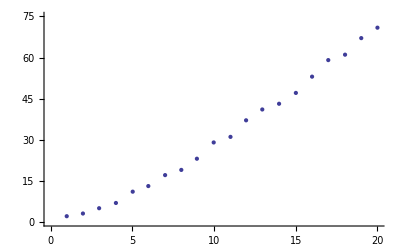

```mathematica
EDAListPlot[Transpose[{xvalues,yvalues}],PlotRange->{{0,20},{0,75}}]
```